```mathematica
RootFinder[m_,β_]:={(sol=NSolve[D[-m^2/4 ϕ^2+β/4 Log[ϕ] ϕ^4,ϕ]==0,ϕ,Reals]);
ran=(ϕ/. sol//Last);
Plot[-m^2/2 ϕ^2+β Log[ϕ] ϕ^4,{ϕ,0,ran}];
(ϕ1=ϕ/. sol[[1]]);
(ϕ2=ϕ/. sol[[2]]);
(Δϕi=Abs[ϕ1-ϕ2]);}

mcritfinder[β_]:={m[0]=0.0001;
RootFinder[m[0],β];
Δϕ[0]=Δϕi;
m[1]=m[0]+0.001;
ind=1;
Do[{If[ind==1,{RootFinder[m[n],β];
(Δϕ[n]=Δϕi);
If[Δϕ[n]<Δϕ[n-1],m[n+1]=m[n]+0.001,m[n+1]=m[n]-0.001];
If[Length[ϕ/. sol]<2,ind=0;Print[{n,m[n]}],Null];},Null]},{n,1,500}]}
```

```mathematica
mcritfinder[-0.1]
```

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{212,0.2121}

{Null}

```mathematica
mcritfinder2D[mi_,βi_]:={m[0]=mi;
β[0]=βi;
RootFinder[m[0],β[0]];
Δϕ[0]=Δϕi;
m[1]=m[0]+0.001;
β[1]=β[0]+0.001;
ind=1;
step=0.01;
Do[{If[ind==1,{RootFinder[m[n],β[n-1]];
Δϕm[n]=Δϕi;
RootFinder[m[n-1],β[n]];
Δϕβ[n]=Δϕi;
If[Δϕm[n]<Δϕ[n-1],m[n+1]=m[n]+step,m[n+1]=m[n]-step];
If[Δϕβ[n]<Δϕ[n-1],β[n+1]=β[n]+step,β[n+1]=β[n]-step];
RootFinder[m[n],β[n]];
Δϕ[n]=Δϕi;
If[Length[ϕ/. sol]<2,ind=0;nf=n-1;mf=m[n-1];βf=β[n-1];Print[{n-1,mf,βf}];,Null];},Null]},{n,1,500}]}
```

```mathematica
mcritfinder2D[0.02,-0.3]
```

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

{158,0.178,-0.142}

{Null}

```mathematica
mf^2/Abs[βf]
```

0.223127

```mathematica
N[Exp[-3/2]]
```

0.22313

```mathematica
mcritfinder2D[0.1,-0.1]
```

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

{27,0.127,-0.073}

{Null}

```mathematica
mf^2/Abs[βf]
```

0.220945

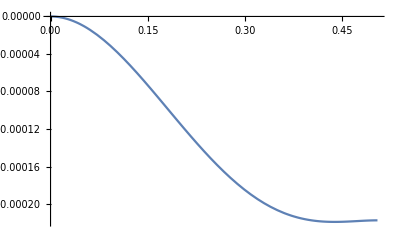

```mathematica
RootFinder[mf,βf];
Plot[(-m^2/4 ϕ^2+β/4 Log[ϕ] ϕ^4)/.{m->mf,β->βf},{ϕ,0,ran}]
```

```mathematica
mcritfinder2D[0.1,0.1]
```

Part::partw: Part 2 of {{ϕ→0.809116}} does not exist.

ReplaceAll::reps: {{{ϕ→0.809116}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{ϕ→0.809693}} does not exist.

ReplaceAll::reps: {{{ϕ→0.809693}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{ϕ→0.808832}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{ϕ→0.808832}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{0,0.1,0.1}

{Null}

```mathematica
betagrid=Array[#&,10,{-1.,-0.001}];
mgrid=Array[#&,10,{0.,0.5}];
```

```mathematica
res={};
Do[Do[mcritfinder2D[mgrid[[i]],betagrid[[j]]];
If[nf>0,If[nf<499,AppendTo[res,{mf^2,βf}],Null],Null],{i,1,10}],{j,1,10}]
```

Part::partw: Part 2 of {{ϕ→0.778801}} does not exist.

ReplaceAll::reps: {{{ϕ→0.778801}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{ϕ→0.778801}} does not exist.

ReplaceAll::reps: {{{ϕ→0.778801}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{ϕ→0.778801}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{ϕ→0.778801}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

{32,0.357556,-0.587}

Last::normal: Nonatomic expression expected at position 1 in Last[ϕ].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Plot::plln: Limiting value Last[ϕ] in {ϕ,0,Last[ϕ]} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

{33,0.376556,-0.679}

{29,0.392111,-0.719}

{25,0.407667,-0.759}

{20,0.413222,-0.809}

{16,0.428778,-0.849}

{12,0.444333,-0.889}

{7,0.449889,-0.939}

{3,0.465444,-0.979}

{0,0.5,-1.}

{3,0.465444,-0.999}

{31,0.356556,-0.588}

{27,0.372111,-0.628}

{22,0.377667,-0.678}

{18,0.393222,-0.718}

{14,0.408778,-0.758}

{9,0.414333,-0.808}

{5,0.429889,-0.848}

{0,0.444444,-0.889}

{0,0.5,-0.889}

{7,0.449889,-0.928}

{28,0.326556,-0.507}

{24,0.342111,-0.547}

{20,0.357667,-0.587}

{16,0.373222,-0.627}

{11,0.378778,-0.677}

{7,0.394333,-0.717}

{3,0.409889,-0.757}

{0,0.444444,-0.778}

{0,0.5,-0.778}

{3,0.409889,-0.777}

{25,0.296556,-0.426}

{21,0.312111,-0.466}

{17,0.327667,-0.506}

{13,0.343222,-0.546}

{9,0.358778,-0.586}

{4,0.364333,-0.636}

{0,0.388889,-0.667}

{0,0.444444,-0.667}

{0,0.5,-0.667}

{22,0.266556,-0.345}

{18,0.282111,-0.385}

{14,0.297667,-0.425}

{10,0.313222,-0.465}

{6,0.328778,-0.505}

{2,0.344333,-0.545}

{0,0.388889,-0.556}

{0,0.444444,-0.556}

{0,0.5,-0.556}

{2,0.344333,-0.545}

{19,0.236556,-0.264}

{15,0.252111,-0.304}

{11,0.267667,-0.344}

{7,0.283222,-0.384}

{3,0.298778,-0.424}

{0,0.333333,-0.445}

{0,0.388889,-0.445}

{0,0.444444,-0.445}

{0,0.5,-0.445}

{15,0.196556,-0.193}

{12,0.222111,-0.223}

{8,0.237667,-0.263}

{4,0.253222,-0.303}

{0,0.277778,-0.334}

{0,0.333333,-0.334}

{0,0.388889,-0.334}

{0,0.444444,-0.334}

{0,0.5,-0.334}

{7,0.283222,-0.373}

{11,0.156556,-0.122}

{8,0.182111,-0.152}

{4,0.197667,-0.192}

{0,0.222222,-0.223}

{0,0.277778,-0.223}

{0,0.333333,-0.223}

{0,0.388889,-0.223}

{0,0.444444,-0.223}

{0,0.5,-0.223}

{6,0.106556,-0.061}

{3,0.132111,-0.091}

{0,0.166667,-0.112}

{0,0.222222,-0.112}

{0,0.277778,-0.112}

{0,0.333333,-0.112}

{0,0.388889,-0.112}

{0,0.444444,-0.112}

{0,0.5,-0.112}

{0,0.,-0.001}

{0,0.0555556,-0.001}

{0,0.111111,-0.001}

{0,0.166667,-0.001}

{0,0.222222,-0.001}

{0,0.277778,-0.001}

{0,0.333333,-0.001}

{0,0.388889,-0.001}

{0,0.444444,-0.001}

{0,0.5,-0.001}

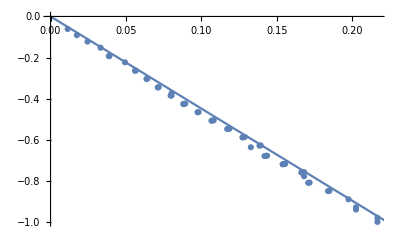

{0.498556,-0.557}

```mathematica
Show[ListPlot[res],
Plot[-Exp[3/2]x,{x,0,0.25}]]
```